```mathematica
ClearAll["Global*'"]
```

```mathematica
Tlist={0.001, 0.00158489 ,0.00251189 ,0.00398107 ,0.00630957 ,0.01, 0.01584893, 0.02511886, 0.03981072, 0.06309573 ,0.1};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.00100000,0.00158489,0.00251189,0.00398107,0.00630957,0.01000000,0.01584893,0.02511886,0.03981072,0.06309573,0.10000000}

```mathematica
plist={3.70, 3.72 ,3.74 ,3.76 ,3.78, 3.80};
pstring=ToString[NumberForm[#,{5,3},ExponentFunction->(Null&)]]&/@plist
```

{3.700,3.720,3.740,3.760,3.780,3.800}

```mathematica
datasets=Table[Table[Import[StringJoin["/Users/chengling/Learning/Research/G_T/cellGPU/testData/preliminary_N900_p",pstring[[p]],"_T",Tstring[[T]],"_time5000000.nc"],"Data"],{T,Length[Tstring]}],{p,Length[pstring]}];
```

```mathematica
data=Import["/Users/chengling/Learning/Research/G_T/cellGPU/testData/preliminary_N900_p3.740_T0.00158489_time5000000.nc","Datasets"]
```

{/BoxMatrix,/d2Edgammadgamma,/energy,/sigma}

```mathematica
|
```

```mathematica
area=datasets[[1,1]][[1,1]][[4]]*datasets[[1,1]][[1,1]][[4]];
```

```mathematica
p380=Table[1/area ()]
```

```mathematica
datasets[[6,9]][[4,4999]][[1]]
```

-0.00200536

```mathematica
Gp380=Table[Table[datasets[[4,T]][[2,i]][[1]],{i,10001,50000}],{T,Length[Tstring]}];
```

```mathematica
Sigmap380=Table[Table[datasets[[4,T]][[4,i]][[1]]*area,{i,10001,50000}],{T,Length[Tstring]}];
```

```mathematica
varsig=Table[Variance[Sigmap380[[T]]],{T,Length[Tstring]}]
```

{0.0648612,0.109209,0.164519,0.270004,0.618686,2.02598,4.74962,9.16796,17.4679,32.6609,60.3498}

```mathematica
meanG=Table[Mean[Gp380[[T]]],{T,Length[Tstring]}]
```

{74.5427,78.3323,94.2436,112.428,155.484,209.656,318.855,418.679,534.609,673.418,837.885}

```mathematica
G=Table[1/area*(meanG[[i]]-varsig[[i]]/Tlist[[i]]),{i,Length[Tlist]}]
```

{0.0107573,0.0104733,0.0319418,0.0495629,0.0638095,0.00784141,0.0213052,0.0596623,0.106482,0.173086,0.26043}

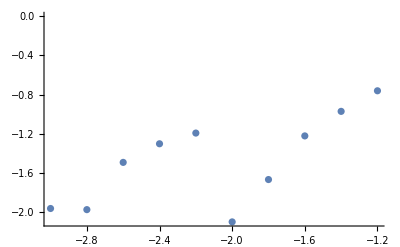

```mathematica
ListPlot[Table[{Log10[Tlist[[i]]],Log10[G[[i]]]},{i,10}]]
```

```mathematica
Max[Sigmap380[[11]]]
```

2.77539×10^6